```mathematica
<<ToMatlab`
```

```mathematica
g[{x_,y_,θ_}]:={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
Unhatξ[ξ_]:={ξ⟦1,3⟧,ξ⟦2,3⟧,-ξ⟦1,2⟧}
```

```mathematica
mBody = 20;
mLink = 0.1;
rBody=0.2;
lLink1 = 1;
lLink2 = 0.5;
inertiaBody = {{mBody,0,0},{0,mBody,0},{0,0,mBody* rBody^2}};
inertiaLink = {{mLink,0,0},{0,mLink,0},{0,0,mLink * lLink^2/12}};
```

```mathematica
g11= g[{0,0,θ11[t]}].g[{lLink1/2, 0, 0}]//FullSimplify;
g12=g11.g[{lLink1/2, 0, 0}].g[{0,0,θ12[t]}].g[{lLink2/2, 0, 0}]//FullSimplify;
g13=g12.g[{lLink2/2, 0, 0}].g[{0,0,θ13[t]}].g[{rBody/2, 0, 0}]//FullSimplify;
g21 = g[{0,0,θ21[t]}].g[{lLink1/2, 0, 0}]//FullSimplify;
g22 = g21.g[{lLink1/2, 0, 0}].g[{0,0,θ22[t]}].g[{lLink2/2, 0, 0}]//FullSimplify;
g23 = g22.g[{lLink2/2, 0, 0}].g[{0,0,θ23[t]}].g[{rBody/2, 0, 0}]//FullSimplify;
```

```mathematica
g11D=g[{0,0,θ11[t]}].g[{lLink1, 0, 0}]//FullSimplify;
g12D=g11D.g[{0,0,θ12[t]}].g[{lLink2, 0, 0}]//FullSimplify;
g13D=g12D.g[{0,0,θ13[t]}].g[{rBody, 0, 0}]//FullSimplify;
g21D=g[{0,0,θ21[t]}].g[{lLink1, 0, 0}]//FullSimplify;
g22D=g21D.g[{0,0,θ22[t]}].g[{lLink2, 0, 0}]//FullSimplify;
g23D=g22D.g[{0,0,θ23[t]}].g[{rBody, 0, 0}]//FullSimplify;
(*(-0.3+0.5+π/2-0.2)-(0.3-0.5-π/2+0.2)*)
```

```mathematica
draw1[θ1_]:=Graphics[{Thickness[0.02],Line[{{0,0},g11D⟦1;;2,3⟧,g12D⟦1;;2,3⟧,g13D⟦1;;2,3⟧}/.{θ11[t]->θ1⟦1⟧,θ12[t]->θ1⟦2⟧,θ13[t]->θ1⟦3⟧}]}];
draw2[θ2_]:=Graphics[{Thickness[0.02],Line[{{0,0},g21D⟦1;;2,3⟧,g22D⟦1;;2,3⟧,g23D⟦1;;2,3⟧}/.{θ21[t]->θ2⟦1⟧,θ22[t]->θ2⟦2⟧,θ23[t]->θ2⟦3⟧}]}];
drawLeg[θ1_,θ2_]:=Show[draw1[θ1],draw2[θ2],PlotRange->{{-1.2,1.2},{-0.1,1.5}}]
```

```mathematica
(* This set of functions sets up a gradient descent that allows initial conditions to be specified and then a local minimum shape configuration to be solved for -- where the local minimum configuration satisfies the constriants *)
Jtmp[θ_]:=Join[g13D⟦1;;2,3⟧-g23D⟦1;;2,3⟧,{π-((θ⟦1⟧+θ⟦2⟧+θ⟦3⟧)-(θ⟦4⟧+θ⟦5⟧+θ⟦6⟧))}]
JEval[θ_]:=(Jtmp[θ].Jtmp[θ])/.{θ11[t]->θ⟦1⟧,θ12[t]->θ⟦2⟧,θ13[t]->θ⟦3⟧,θ21[t]->θ⟦4⟧,θ22[t]->θ⟦5⟧,θ23[t]->θ⟦6⟧}
DJtmp={D[JEval[{θ1,θ2,θ3,θ4,θ5,θ6}],θ1],D[JEval[{θ1,θ2,θ3,θ4,θ5,θ6}],θ2],D[JEval[{θ1,θ2,θ3,θ4,θ5,θ6}],θ3],D[JEval[{θ1,θ2,θ3,θ4,θ5,θ6}],θ4],D[JEval[{θ1,θ2,θ3,θ4,θ5,θ6}],θ5],D[JEval[{θ1,θ2,θ3,θ4,θ5,θ6}],θ6]};
DJEval[θ_]:=DJtmp/.{θ1->θ⟦1⟧,θ2->θ⟦2⟧,θ3->θ⟦3⟧,θ4->θ⟦4⟧,θ5->θ⟦5⟧,θ6->θ⟦6⟧}
```

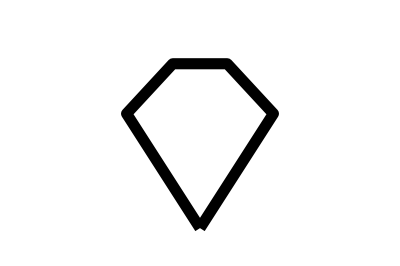

```mathematica
(* VI: define your theta offset!*)
θOffset = {Pi/2-0.56936,1.31465,0.825505,Pi/2+0.56936,-1.31465,-0.825505};
θIK=θOffset;
(* You need to wrap a loop around this to iterate -- or just manually loop *)
drawLeg[θIK⟦1;;3⟧,θIK⟦4;;6⟧]
```

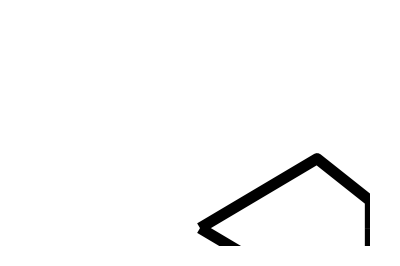

```mathematica
α=0.1;
θInit={.4,0.3,-0.6,-.4,-0.3,0.6};
θout=Table[θInit=θInit-α*DJEval[θInit],{i,1,100}]; (* θout. stores the descent step values *)
drawLeg[θout⟦100,1;;3⟧,θout⟦100,4;;6⟧]
```

```mathematica
ξ11=Unhatξ[Inverse[g11].D[g11,t]]//FullSimplify;
ξ12=Unhatξ[Inverse[g12].D[g12,t]]//FullSimplify;
ξ13=Unhatξ[Inverse[g13].D[g13,t]]//FullSimplify;
ξ21=Unhatξ[Inverse[g21].D[g21,t]]//FullSimplify;
ξ22=Unhatξ[Inverse[g22].D[g22,t]]//FullSimplify;
ξ23=Unhatξ[Inverse[g23].D[g23,t]]//FullSimplify;
```

```mathematica
(* Just treating everything as point masses, but this will not effect the results *)
MLink={{mLink,0,0},{0,mLink,0},{0,0,mLink*lLink1^2}};
MBody={{mBody,0,0},{0,mBody,0},{0,0,mBody*rBody^2}};
```

```mathematica
KE=1/2*(ξ11.MLink.ξ11+ξ12.MLink.ξ12+ξ13.MBody.ξ13+ξ21.MLink.ξ21+ξ22.MLink.ξ22+ξ23.MBody.ξ23)//FullSimplify;
PE=9.8*(mLink*g11⟦2,3⟧+mLink*g12⟦2,3⟧+mBody*g13⟦2,3⟧+mLink*g21⟦2,3⟧+mLink*g22⟦2,3⟧+mBody*g23⟦2,3⟧)//FullSimplify;
L=KE-PE//FullSimplify;
q={θ11[t],θ12[t],θ13[t],θ21[t],θ22[t],θ23[t]};
Dq=D[q,t];
```

```mathematica
Mq=FullSimplify[Outer[D,FullSimplify[Outer[D,{L},D[q,t]]]⟦1⟧,D[q,t]]]//Chop;
Cq=FullSimplify[FullSimplify[Outer[D,FullSimplify[Outer[D,{L},D[q,t]]]⟦1⟧,q]].D[q,t]-Outer[D,{KE},q]⟦1⟧]//Chop;
gq = FullSimplify[Outer[D,{PE},q]]⟦1⟧//Chop;
```

```mathematica
Γ[i_,j_,k_]:=1/2(D[Mq⟦i,j⟧,q⟦k⟧]+D[Mq⟦i,k⟧,q⟦j⟧]-D[Mq⟦k,j⟧,q⟦i⟧]);
Cij[i_,j_]:=Sum[Γ[k,i,j]*Dq⟦k⟧,{k,1,6}];
CMatrix=FullSimplify[Table[Cij[i,j],{i,1,6},{j,1,6}]]//Chop;
Bq = {{0 , 0}, {0 , 0},{1 , 0},{0 , 0},{0 , 0},{0 , 1}};
Bq //MatrixForm;
```

```mathematica
constraints=Join[g13D⟦1;;2,3⟧-g23D⟦1;;2,3⟧,{π-((θ11[t]+θ12[t]+θ13[t])-(θ21[t]+θ22[t]+θ23[t]))}];
Aq=FullSimplify[Outer[D,constraints,q]];
DAqt=D[Aq,t];
Aq //MatrixForm;
Dimensions[Aq];
```

## Calculate the similarity transformation matrix H

```mathematica
Dhθ1 = Aq[[1;;3,1;;3]];
Dhθ2 = Aq[[1;;3,4;;6]];
Hq = -Inverse[Dhθ1].Dhθ2;
Hq //MatrixForm;
HDotq = D[Hq,t];
```

## Create functions to save in Matlab

```mathematica
(* Need to rename variables for Matlab *)
MqMatlab=Mq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
CqMatlab=Cq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23,θ11'[t]->Dtheta11,θ12'[t]->Dtheta12,θ13'[t]->Dtheta13,θ21'[t]->Dtheta21,θ22'[t]->Dtheta22,θ23'[t]->Dtheta23}//Chop;
CMatrixMatlab=CMatrix/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23,θ11'[t]->Dtheta11,θ12'[t]->Dtheta12,θ13'[t]->Dtheta13,θ21'[t]->Dtheta21,θ22'[t]->Dtheta22,θ23'[t]->Dtheta23}//Chop;
gqMatlab=gq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
AqMatlab=Aq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
DAqMatlab=DAqt/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23,θ11'[t]->Dtheta11,θ12'[t]->Dtheta12,θ13'[t]->Dtheta13,θ21'[t]->Dtheta21,θ22'[t]->Dtheta22,θ23'[t]->Dtheta23}//Chop;
g13DMatlab= g13DO/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
g23DMatlab= g23DO/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
DgqMatlab = Dgq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
HqMatlab = Hq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
HDotqMatlab = HDot/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23,θ11'[t]->Dtheta11,θ12'[t]->Dtheta12,θ13'[t]->Dtheta13,θ21'[t]->Dtheta21,θ22'[t]->Dtheta22,θ23'[t]->Dtheta23}//Chop;
constraintsMatlab = constraints/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
```

Dgq

## Calculate transformed matrices

```mathematica
Dimensions[Join[Hq,IdentityMatrix[3]]];
```

```mathematica
Mhatq = Transpose[Join[Hq,IdentityMatrix[3]]].Mq.Join[Hq, IdentityMatrix[3]]; 
Mhatq //MatrixForm;
Dimensions[Mhatq];

Ghatq =  Transpose[Join[Hq,IdentityMatrix[3]]].gq //FullSimplify;
Dimensions[Ghatq];
Ghatq //MatrixForm;
DGHatq = FullSimplify[Outer[D,Ghatq,q]];

DGHatq = DGHatq[[1;;3,1;;3]];
DGHatqMatlab = DGHatq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
Dimensions[DGHatq];
DGHatqMatlab //MatrixForm;

Dgq = FullSimplify[Outer[D,gq,q]];
DgqMatlab = Dgq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
Dimensions[Dgq];
DgqMatlab //MatrixForm;

Chatq = Transpose[Join[Hq,IdentityMatrix[3]]].Mq.Join[HDotq, {{0, 0, 0},{0, 0, 0},{0, 0, 0}}] +  Transpose[Join[Hq,IdentityMatrix[3]]].CMatrix.Join[Hq, IdentityMatrix[3]]; //FullSimplify
Dimensions[Chatq];
Bhatq =  Transpose[Join[Hq,IdentityMatrix[3]]].Bq //FullSimplify;
Dimensions[Bhatq];
Bhatq //MatrixForm;

DBHat1q = FullSimplify[Outer[D,Bhatq[[1;;3,1]],q]];
DBHat1q = DBHat1q[[1;;3,1;;3]];
DBHat1q //MatrixForm;
DBHat2q = FullSimplify[Outer[D,Bhatq[[1;;3,2]],q]];
DBHat2q = DBHat2q[[1;;3,1;;3]];
DBHat2q //MatrixForm;
DBHat1qMatlab = DBHat1q/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
DBHat2qMatlab = DBHat2q/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
Dimensions[DBHat1q];
Dimensions[DBHat2q];

Bq //MatrixForm 
DB1q = FullSimplify[Outer[D,Bq[[1;;6,1]],q]];
DB1q //MatrixForm;
DB2q = FullSimplify[Outer[D,Bq[[1;;6,2]],q]];
DB2q //MatrixForm
DB1qMatlab = DB1q/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
DB2qMatlab = DB2q/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
```

((2. Cos[θ11[t]-θ21[t]]+1. Cos[θ11[t]-θ21[t]-θ22[t]]+0.4 Cos[θ11[t]-θ21[t]-θ22[t]-θ23[t]]) Csc[θ12[t]] | Csc[θ12[t]] (0.4 Cos[θ12[t]+θ13[t]]+Cot[θ12[t]] (-0.4 Sin[θ12[t]+θ13[t]]-2. Sin[θ11[t]-θ21[t]]-1. Sin[θ11[t]-θ21[t]-θ22[t]]-0.4 Sin[θ11[t]-θ21[t]-θ22[t]-θ23[t]])) | 0.4 Cos[θ12[t]+θ13[t]] Csc[θ12[t]]
(1. Cos[θ11[t]-θ21[t]-θ22[t]]+0.4 Cos[θ11[t]-θ21[t]-θ22[t]-θ23[t]]) Csc[θ12[t]] | Csc[θ12[t]] (0.4 Cos[θ12[t]+θ13[t]]+Cot[θ12[t]] (-0.4 Sin[θ12[t]+θ13[t]]-1. Sin[θ11[t]-θ21[t]-θ22[t]]-0.4 Sin[θ11[t]-θ21[t]-θ22[t]-θ23[t]])) | 0.4 Cos[θ12[t]+θ13[t]] Csc[θ12[t]]
0.4 Cos[θ11[t]-θ21[t]-θ22[t]-θ23[t]] Csc[θ12[t]] | Csc[θ12[t]] (0.4 Cos[θ12[t]+θ13[t]]+Cot[θ12[t]] (-0.4 Sin[θ12[t]+θ13[t]]-0.4 Sin[θ11[t]-θ21[t]-θ22[t]-θ23[t]])) | 0.4 Cos[θ12[t]+θ13[t]] Csc[θ12[t]])

(0 | 0
0 | 0
1 | 0
0 | 0
0 | 0
0 | 1)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

## Save untransformed functions to Matlab

```mathematica
(* Easier to just write directly to file, then copy and paste the resulting expression in the .m file where the functions are defined *)
fMq=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\MqQ.m"]
WriteMatlab[MqMatlab,fMq];
Close[fMq];
```

OutputStream[…]

```mathematica
SystemOpen["C:\\Users\\Puneet\\Documents\\Research\\goatProject\\Dynamic_Modelling\\derivation_correct_rotation\\MATHSource\\MqQ.m"]
```

```mathematica
fCq=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\CqQ.m"]
WriteMatlab[CqMatlab,fCq];
Close[fCq];
```

OutputStream[…]

```mathematica
fgq=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\gqQ.m"]
WriteMatlab[gqMatlab,fgq];
Close[fgq];
```

OutputStream[…]

```mathematica
fAq=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\AqQ.m"]
WriteMatlab[AqMatlab,fAq];
Close[fAq];
```

OutputStream[…]

```mathematica
fDaq=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\Daq.m"]
WriteMatlab[DAqMatlab,fDaq];
Close[fDaq];
```

OutputStream[…]

```mathematica
fg13=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\g13Q.m"]
WriteMatlab[g13DMatlab,fg13];
Close[fg13];
```

OutputStream[…]

```mathematica
fg23=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\g23Q.m"]
WriteMatlab[g23DMatlab,fg23];
Close[fg23];
```

OutputStream[…]

```mathematica
fCM=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\CMQ.m"]
WriteMatlab[CMatrixMatlab,fCM];
Close[fCM];
```

OutputStream[…]

```mathematica
fHQ=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\HQ.m"]
WriteMatlab[HqMatlab,fHQ];
Close[fHQ];
```

OutputStream[…]

```mathematica
fHDotQ=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\HDotQ.m"]
WriteMatlab[HDotqMatlab,fHDotQ];
Close[fHDotQ];
```

OutputStream[…]

```mathematica
fcontraintsQ=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\contraintsQ.m"]
WriteMatlab[constraintsMatlab,fcontraintsQ];
Close[fcontraintsQ];
```

OutputStream[…]

## Save transformed functions to Matlab

```mathematica
MhatMatlab = Mhatq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
fCM=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\MhatQ.m"]
WriteMatlab[MhatMatlab,fCM];
Close[fCM];
```

OutputStream[…]

```mathematica
GhatMatlab = Ghatq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
fCM=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\GhatQ.m"]
WriteMatlab[GhatMatlab,fCM];
Close[fCM];
```

OutputStream[…]

```mathematica
ChatMatlab = Chatq/.{θ11[t]->theta11,θ12[t]->theta12,θ13[t]->theta13,θ21[t]->theta21,θ22[t]->theta22,θ23[t]->theta23}//Chop;
fCM=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\ChatQ.m"]
WriteMatlab[ChatMatlab,fCM];
Close[fCM];
```

OutputStream[…]

```mathematica
fCM=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\BhatQ.m"]
WriteMatlab[Bhat,fCM];
Close[fCM];
```

OutputStream[…]

```mathematica
fDg=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\DGQ.m"]
WriteMatlab[DgqMatlab,fDg];
Close[fDg];
```

OutputStream[…]

```mathematica
fDB1=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\DB1Q.m"]
WriteMatlab[DB1qMatlab,fDB1];
Close[fDB1];
```

OutputStream[…]

```mathematica
fDB2=OpenWrite["C:\\Users\\Puneet\\Documents\\GitHub\\model_predictive_control\\goat2D_fullStates_mpc\\MATHSource\\DB2Q.m"]
WriteMatlab[DB2qMatlab,fDB2];
Close[fDB2];
```

OutputStream[…]